```mathematica
ClearAll["Global`*"]
```

# -Graphics-

Plot options and export function

```mathematica
figpath[filename_]:=StringTemplate["/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures/``.pdf"][filename];
export[object_,name_]:=Export[figpath[name],object/. {EdgeForm[],r_?(MemberQ[{RGBColor,Hue,CMYKColor,GrayLevel},Head[#]]&),i___}:>{EdgeForm[r],r,i},ImageResolution->1500];
```

```mathematica
j0=11/2;
theta0=70*π/180;
j1=j0*Cos[theta0];
j2=j0*Sin[theta0];
moi1=10;
moi2=20;
moi3=40;
A1Const=1/(2*moi1);
A2Const=1/(2*moi2);
A3Const=1/(2*moi3);
```

```mathematica
x1[I_,theta_,phi_]:=I*Sin[theta]*Cos[phi];
x2[I_,theta_,phi_]:=I*Sin[theta]*Sin[phi];
x3[I_,theta_,phi_]:=I*Cos[theta];
A[I_]:=A2Const*(1-j2/I)-A1Const;
u[I_]:=(A3Const-A1Const)/A[I];
v0[I_]:=(-A1Const*j1)/A[I];
```

Classical energy function H’

```mathematica
Hprime[I_,theta_,phi_]:=x2[I,theta,phi]^2+u[I]*x3[I,theta,phi]^2+2*v0[I]*x1[I,theta,phi];
Hprime[I_,theta_,phi_]:=x3[I,theta,phi]^2(u[I]-Sin[phi]^2-v0[I]/I Cos[phi])+I^2 Sin[phi]^2+2v0[I]*I*Cos[phi];
```

Minimum points

```mathematica
(*absolute minimum *)
min1=Values@FindMinimum[{Hprime[19/2,x,y],x>1&&x<π&&y>0&&y<1},{x,y}][[2]];
min2=Values@FindMinimum[{Hprime[19/2,x,y],x>1&&x<π&&y>5&&y<2π},{x,y}][[2]];
min3=Values@FindMinimum[{Hprime[19/2,x,y],x>1&&x<π&&y>2&&y<4},{x,y}][[2]];
max1=Values@FindMaximum[{Hprime[19/2,π/2,y],y>0.5&&y<2},{y}][[2,1]];
max2=Values@FindMaximum[{Hprime[19/2,π/2,y],y>4&&y<2π},{y}][[2,1]];
```

```mathematica
(* Trick for custom ticks *)
(* source: https://mathematica.stackexchange.com/questions/190490/add-minor-ticks-to-custom-ticks?noredirect=1&lq=1 *)
tickFuncText[x_,y_]:=Join[{#,#,{.03,0}}&/@Subdivide[y,x],{#," ",{.01,0}}&/@Subdivide[##,5*x]]&;
tickFuncMute[x_,y_]:=Join[{#," ",{.03,0}}&/@Subdivide[y,x],{#," ",{.01,0}}&/@Subdivide[##,5*x]]&;
```

The contour plot function definition

```mathematica
cp[I_]:=ContourPlot[
Hprime[I,theta,phi],{theta,0,π},{phi,0,2π},
AspectRatio->Automatic,
Contours->19,
Frame->True,
FrameStyle->Directive[Black,Thick],PlotRangePadding->None,
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},PlotLegends->BarLegend[Automatic,None,LegendLabel->Style["H'(θ_3,φ_3)\n[MeV]",Italic]],
FrameLabel->{"θ_3 [rad]","φ_3 [rad]"},
FrameTicks->{{Automatic,Automatic},{tickFuncText[3,3],tickFuncMute[3,3]}},
ImageSize->280,
ColorFunction->"BlueGreenYellow"
];
```

The minimum points for the energy function

```mathematica
point1=Graphics[{PointSize[0.07],Red,Point[min1],Text[Style["m",19,Red,Bold,FontFamily->"Latin Modern Roman"],{1.2,6}]}];
point2=Graphics[{PointSize[0.07],Red,Point[min2],Text[Style["m",19,Red,Bold,FontFamily->"Latin Modern Roman"],{1.2,3}]}];
point3=Graphics[{PointSize[Large],Magenta,Point[{π/2,max1}],Text[Style["M",19,Magenta,Bold,FontFamily->"Latin Modern Roman"],{1.9,5}]}];
point4=Graphics[{PointSize[Large],Magenta,Point[{π/2,max2}],Text[Style["M",19,Magenta,Bold,FontFamily->"Latin Modern Roman"],{1.9,1.2}]}];
point5=Graphics[{PointSize[Large],Red,Point[min3],Text[Style["m",19,Red,Bold,FontFamily->"Latin Modern Roman"],{1.2,0.5}]}];
```

Contour plot

```mathematica
Show[cp[19/2],point1,point2,point3,point4,point5]
export[Show[cp[19/2],point1,point2,point3,point4,point5],"New-Boson-Classical-H-3axis-quantization"];
```

-Graphics-

Energy plot for H’ as function of φ_2

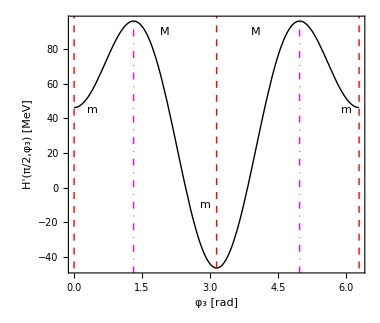

```mathematica
(* sources for adding colored lines inside an Epilog function *)
(* source1: https://mathematica.stackexchange.com/questions/3561/how-to-add-a-vertical-line-to-a-plot *)
(* source2: https://mathematica.stackexchange.com/questions/20218/how-to-color-lines-in-epilog *)
plot1=Plot[
Hprime[19/2,π/2,x],{x,0,2π},
Frame->True,Axes->False,AspectRatio->0.85,ImageSize->380,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
FrameLabel->{"φ_3 [rad]","H'(π/2,φ_3) [MeV]"},
Epilog->{
{Red,Dashed,Thick,Line[{{min1[[2]],-100},{min1[[2]],200}}]},
{Red,Dashed,Thick,Line[{{min2[[2]],-100},{min2[[2]],200}}]},
{Red,Dashed,Thick,Line[{{min3[[2]],-100},{min3[[2]],200}}]},
{Magenta,DotDashed,Thick,Line[{{max1,-100},{max1,200}}]},{Magenta,DotDashed,Thick,Line[{{max2,-100},{max2,200}}]},{Style[Text["M",{2,90}],Magenta,Bold,19,FontFamily->"Latin Modern Roman"]},{Style[Text["M",{4,90}],Magenta,19,Bold,FontFamily->"Latin Modern Roman"]},
{Style[Text["m",{0.4,45}],Red,Bold,19,FontFamily->"Latin Modern Roman"]},
{Style[Text["m",{2.9,-10}],Red,Bold,19,FontFamily->"Latin Modern Roman"]},
{Style[Text["m",{6,45}],Red,Bold,19,FontFamily->"Latin Modern Roman"]}
}
];
Show[plot1]
export[plot1,"New-Boson-Classical-H-3-axis-varphi-plot"];
```

Numerical tests for the classical energy function

```mathematica
linspace[x_,y_,n_]:=N@Subdivide[x,y,n-1];
theta2values=linspace[0,π,5];
phi2values=linspace[0,2π,5];
spin=19/2;
Do[
theta2=theta2values[[i]];
phi2i=phi2values[[i]];
hprime=Hprime[spin,theta2,phi2i];
Print[theta2," ",phi2i," ",hprime],
{i,1,Length[theta2values]}]
```

0. 0. 110.824

0.785398 1.5708 88.9631

1.5708 3.14159 -46.2958

2.35619 4.71239 88.9631

3.14159 6.28319 110.824